```mathematica
Quit
```

# Examples of Multi-Field Vacuum Decay

This tutorial contains examples of false vacuum decay in potential with multiple scalar fields computed with Polygonal Bounces approach.

Loads the package

```mathematica
SetDirectory[FileNameTake[NotebookDirectory[],{1,-4}]];
<<"FindBounce.m"
```

## False vacuum decay

## Single Field Potential

### Potential

```mathematica
U1[ϕ_]:=Block[{αs = .9,V},V = 1/2(ϕ)^2-1/2(ϕ)^3+αs/8 (ϕ)^4 ];
Extrema1=Block[{φ},φ/.Sort@NSolve[(D[U1[φ],φ])==0,φ]];
plotU = Plot[U1[Extrema1[[3]]-ϕ],{ϕ,0,Extrema1[[3]]},PlotStyle->{Black,Dashed}];
```

### Bounce

```mathematica
PB1 =  FindBounce[ U1[ϕ],ϕ,{Extrema1[[1]],Extrema1[[3]]}];
```

### Plot

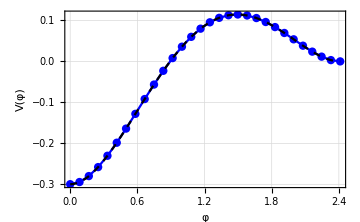
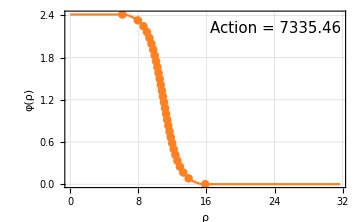

```mathematica
plot1 =PlotBounce[PB1];
Row[{Show[{plot1[[1]],plotU }],plot1[[2]]}]
```

### -Options

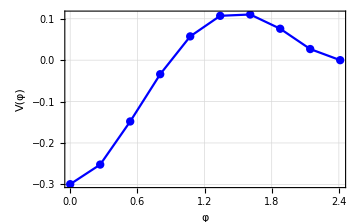
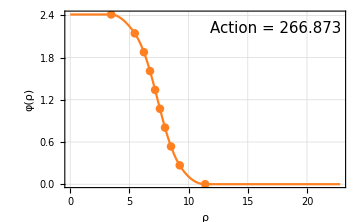

```mathematica
(*Derivative of U1*)
dU1[ϕ_]:=Block[{αs=.9,V},V= ϕ-(3 ϕ^2)/2+(αs ϕ^3)/2];
(*Bounce*)
PB1 =  FindBounce[ U1[φ],{φ},Extrema1[[{1,3}]],  "NumberSegments"->9, "Dimension"->3,Gradient-> dU1[φ],"AccuracyBounce"->4,"AnsatzRadii"->10 ];
(*Plot*)
Row[PlotBounce[PB1]]
```

## >Two Field Potential

### Potential

```mathematica
μλαϵ={{80.,100.},{.1,.3},2.,{0.,0.}} ;
rangeU={-16000,1000};
Extrema2 = {{0,12.9099},{6.25901,6.00687},{20.,0.}};
Potential2[ϕ_]:=Sum[-μλαϵ[[1,i]] (ϕ[[i]])^2 +μλαϵ[[2,i]](ϕ[[i]])^4+μλαϵ[[4,i]]ϕ[[i]] ,{i,1,2}]+ μλαϵ[[3]](ϕ[[1]])^2 (ϕ[[2]])^2; 
φs2 = {φ1,φ2};
contourV = ContourPlot[ Potential2[{ϕ1,ϕ2}],{ϕ1,-1,21},{ϕ2,-1,Extrema2[[1,2]]+1},PlotRange->rangeU,ContourShading->None,GridLines->Automatic,Contours->50,GridLinesStyle->Directive[Dashed,GrayLevel[.85]],ContourStyle->Opacity[0.4],FrameLabel->{"φ_1","φ_2"},ImageSize->400,LabelStyle->Directive[Black,FontSize->25, FontFamily->"Times New Roman",FontSlant->Plain] ];
```

### Bounce

```mathematica
Block[{time},
{time,PB2} =FindBounce[Potential2[φs2],{φ1,φ2},Extrema2[[{1,3}]],"InitialFieldValue"->Extrema2[[2]]]//AbsoluteTiming;
Row[{"Total time consumed = ",time," s."}]  ]
```

Total time consumed = 0.134515 s.

### Plot

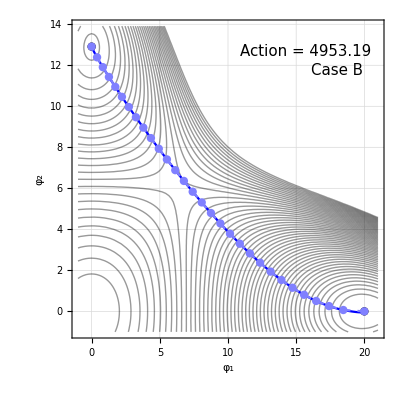
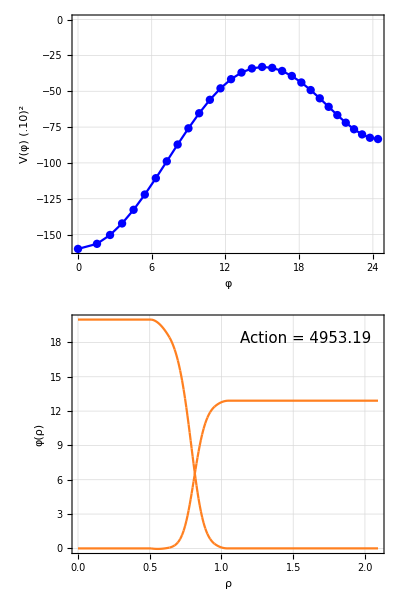

```mathematica
pBounce2 = PlotBounce2D[PB2];
plot2 = {Show[contourV,pBounce2[[1]] ,PlotRange->All,ImageSize->400,Epilog->{{Text[Style[Row[{"Action = ",BounceAction[PB2]}],10,15,"Times New Roman"],Scaled[{0.75,0.9}],Background->LightGreen]},{Text[Style["Case B",10,15,"Times New Roman"],Scaled[{0.85,0.84}],Background->LightRed]}}],
Column[pBounce2[[2;;3]]]};Row[plot2]
```

## >Three Field Potential

### The Potential

#### Minima

```mathematica
{typeV,Extrema3,parameters3}=Block[{μ1=40,μ2=100,μ3=120,λ1=.1,λ2=.2,λ3=.3,α1=2,α2=2.1,α3=1.2,ϵ1 =100,ϵ2 = 150,ϵ3 = 100,V,Φ,ϕ1,ϕ2,ϕ3,dV,d2V,sols,typeV,Extrema,ExtremaAnsatz,singEig ,parameters3},
V[ϕ_] := -μ1 (ϕ[[1]])^2-μ2 (ϕ[[2]])^2-μ3 (ϕ[[3]])^2 +λ1 (ϕ[[1]])^4+λ2 (ϕ[[2]])^4+λ3 (ϕ[[3]])^4+ α1 (ϕ[[1]])^2 (ϕ[[2]])^2+α2 (ϕ[[1]])^2 (ϕ[[3]])^2+α3 (ϕ[[2]])^2 (ϕ[[3]])^2 +ϵ1 ϕ[[1]] +ϵ2 ϕ[[2]] +ϵ3 ϕ[[3]] ;
Φ = {ϕ1,ϕ2,ϕ3};
dV = D[V[Φ],{Φ}];
d2V = D[V[Φ],{Φ},{Φ}];
ExtremaAnsatz={{0.,-15.8113883,0.},{6.54653671,-5.976143,0.},{20.,0.,0.}};
(*Find new minima*)
sols = Table[FindRoot[dV,Transpose@{Φ,ExtremaAnsatz[[i]]}],{i,1,3}];
d2V = D[V[Φ],{Φ},{Φ}]/.sols;
singEig =Table[DeleteDuplicates@Sign[Eigenvalues@d2V[[i]]],{i,1,3}];
(*Classify type of minima*)
typeV = Table[If[Length@singEig[[i]] >1,"Saddle",If[singEig[[i,1]] >0,"Minimum","Maximum"]],{i,1,3}];
Extrema = Φ/.sols;
parameters3 = {μ1,μ2,μ3,λ1,λ2,λ3,α1,α2,α3,ϵ1,ϵ2,ϵ3} ;
{typeV,Extrema,parameters3}//Chop
];
Row[{"type of Minima: ",typeV}]
```

type of Minima: {Minimum,Saddle,Minimum}

#### Potential

```mathematica
Potential3[ϕ_]:=Block[{V,μ1,μ2,μ3,λ1,λ2,λ3,α1,α2,α3,ϵ1,ϵ2,ϵ3},
{μ1,μ2,μ3,λ1,λ2,λ3,α1,α2,α3,ϵ1,ϵ2,ϵ3}=parameters3;
V = -μ1 (ϕ[[1]])^2-μ2 (ϕ[[2]])^2-μ3 (ϕ[[3]])^2 +λ1 (ϕ[[1]])^4+λ2 (ϕ[[2]])^4+λ3 (ϕ[[3]])^4+ α1 (ϕ[[1]])^2 (ϕ[[2]])^2+α2 (ϕ[[1]])^2 (ϕ[[3]])^2+α3 (ϕ[[2]])^2 (ϕ[[3]])^2 +ϵ1 ϕ[[1]] +ϵ2 ϕ[[2]] +ϵ3 ϕ[[3]] ];
φs3 = {φ1,φ2,φ3};
```

#### Plot

```mathematica
plotPotential =Block[{extremaV,triangleV,potential3,plotZ,plot},
triangleV = Graphics3D[{Darker[Red],Thickness[.005],Line[Extrema3]}];
extremaV=ListPointPlot3D[ Extrema3 ,PlotStyle->{Directive[ Orange,PointSize[.02]]}];
potential3  =Show[RegionPlot3D[Potential3[{Φ1,Φ2,Φ3}]<-1500,{Φ1,-1.5,22},{Φ2,-22,2},{Φ3,-2.8,1},PlotStyle->{Directive[Darker[Orange],Opacity[0.5]],Directive[Lighter[Blue],Opacity[0.5]]},Mesh->None,AxesLabel->{"ϕ_1","ϕ_2","ϕ_3"},LabelStyle->Directive[Black,FontSize->25, FontFamily->"Times New Roman",FontSlant->Plain],PlotRange->All,Lighting->"Neutral",Background->None],
triangleV,extremaV];
plotZ =Show[ContourPlot[Potential3[{Φ1,Φ2,-2.5}],{Φ1,-1.5,22},{Φ2,-22,2},Contours->60,GridLines->Automatic,Axes->False,GridLinesStyle->Directive[Dashed,GrayLevel[.85]],ContourStyle->Opacity[0.4],ImageSize->Medium,PlotRangePadding->0,Frame->False,LabelStyle->Directive[Black,FontSize->25, FontFamily->"Times New Roman",FontSlant->Plain]],ListPlot[Transpose@Transpose[Extrema3][[{1,2}]],PlotStyle->{Directive[ Orange,PointSize[.02]]}],ListPlot[Transpose@Transpose[Extrema3][[{1,2}]],PlotStyle->{Red},Joined->True]];
plot = {Show[potential3,PlotRange->All,BoxRatios->{1,1,1},ImageSize->400],plotZ } ];
contourZ[plotZ_Graphics]:=Block[{levelZ,c,projectionZ},
c =PlotRange/.plotZ[[2]];
levelZ=-3.5;
projectionZ=Graphics3D[{Texture[plotZ],EdgeForm[],Polygon[{{c[[1,1]],c[[2,1]],levelZ},{c[[1,2]],c[[2,1]],levelZ},{c[[1,2]],c[[2,2]],levelZ},{c[[1,1]],c[[2,2]],levelZ}},VertexTextureCoordinates->{{0,0},{1,0},{1,1},{0,1}}]},Lighting->"Neutral",ImageSize->400]];
```

### Bounce

```mathematica
Block[{time},
{time,PB3} =FindBounce[Potential3[φs3],φs3,{Extrema3[[1]],Extrema3[[3]]},"InitialFieldValue"->Extrema3[[2]]]//AbsoluteTiming;
Row[{"Total time consumed = ",time," s."}]    ]
```

Total time consumed = 0.178758 s.

### Plot

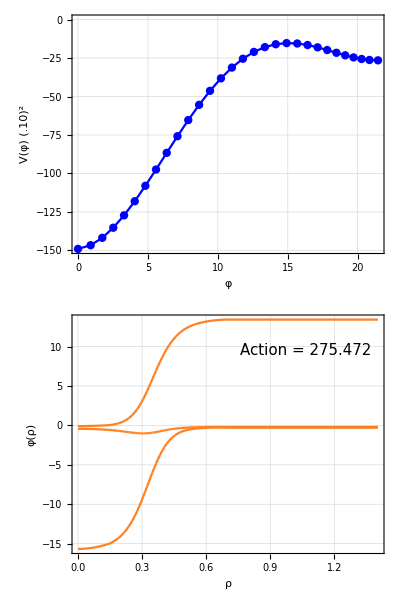
-Graphics3D--Graphics-

```mathematica
pBounce3 = PlotBounce3D[PB3];
plot3 = {Show[{plotPotential[[1]],contourZ[Show[plotPotential[[2]],Show[PlotBounce2DProjection[PB3,{1,2}],Epilog->{{Text[Style[Row[{"Action = ",BounceAction[PB3]}],10,15,"Times New Roman"],Scaled[{0.35,0.92}],Background->LightGreen]},{Text[Style["Case B",10,15,"Times New Roman"],Scaled[{0.25,0.84}],Background->LightRed]}}]]],pBounce3 [[1]]},PlotRange->All,ImageSize->400],
Column[pBounce3[[2;;3]]]};Row[plot3]
```

## All Plots

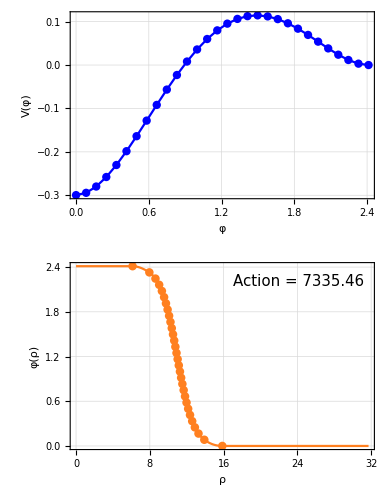
-Graphics--Graphics--Graphics-     -Graphics3D--Graphics-

```mathematica
PLOTS = Magnify[Row[Flatten[{GraphicsGrid[Transpose@{plot1}],plot2,"     ",plot3,"    "}]],.7]
```

```mathematica
(*Export[ FileNameJoin[{FileNameTake[NotebookDirectory[],{1,-5}],"Images","ExaplesBounces.png"}],PLOTS ];*)
```

## Dynamical Examples

## >Single Field Potential

### Plot

```mathematica
ListPlotBounce[pts_List]:=Block[{PB,φV,plot},
	φV = Transpose[pts];
	 CheckAbort[PB =FindBounce[Null,Null,{φV[[1,1]],φV[[1,-1]]},"AnsatzPath"->φV[[1]],"AnsatzV1"->φV[[2]]  ];
			plot =PlotBounce[PB][[2]];  ,
			plot ="$Aborted";];
	Return[plot]   ];
DynamicModule[{pts ={{0.,-0.4},{0.15,-0.3},{0.25,0.3},{0.5,0.7},{0.75,0.3},{1,-0}},d=4,ptsT,PB,plot},
ptsT =Transpose[pts];
CheckAbort[
	plot = ListPlotBounce[pts] ,plot ="$Aborted";];
Row[{LocatorPane[Dynamic[pts],Dynamic[   ListPlot[pts,Joined->True,Mesh->All,PlotRange->{{-0.1,1.1},{Min[ptsT[[2]]] 2,Max[ptsT[[2]]]1.5}},Frame->True,
FrameLabel->{"φ","V(φ)"},GridLines->Automatic,GridLinesStyle->GrayLevel[.85],ImageSize->Medium,MeshStyle->PointSize[Large],LabelStyle->Directive[Black,FontSize->17, FontFamily->"Times New Roman",FontSlant->Plain],PlotStyle->Darker[Blue],Axes->False]      ],Appearance->None],Dynamic[plot] }]]
```

## >Two Field Potential

### Plot

```mathematica
DynamicModule[{μ,λ,αs,ϵ,μλαϵ,Extrema,plot,abort,Action,Potential2,dV,d2V,plots,ϕ1,ϕ2,ϕs,d=4,PB2 ,plot2,pBounce2,Extrema0={{0,12.9099},{6.259,6.00687},{20.,0.}}},
Manipulate[
 μλαϵ={{μ1,μ2},{λ1,λ2},α,{ϵ1,ϵ2}};
(*========================================*)
Potential2[ϕ_]:=μλαϵ⟦3⟧ ϕ⟦1⟧^2 ϕ⟦2⟧^2-ϕ⟦1⟧^2 μλαϵ⟦1,1⟧-ϕ⟦2⟧^2 μλαϵ⟦1,2⟧+ϕ⟦1⟧^4 μλαϵ⟦2,1⟧+ϕ⟦2⟧^4 μλαϵ⟦2,2⟧+ϕ⟦1⟧ μλαϵ⟦4,1⟧+ϕ⟦2⟧ μλαϵ⟦4,2⟧; 
dV[ϕ_]:= {2 μλαϵ⟦3⟧ ϕ⟦1⟧ ϕ⟦2⟧^2-2 ϕ⟦1⟧ μλαϵ⟦1,1⟧+4 ϕ⟦1⟧^3 μλαϵ⟦2,1⟧+μλαϵ⟦4,1⟧,2 μλαϵ⟦3⟧ ϕ⟦1⟧^2 ϕ⟦2⟧-2 ϕ⟦2⟧ μλαϵ⟦1,2⟧+4 ϕ⟦2⟧^3 μλαϵ⟦2,2⟧+μλαϵ⟦4,2⟧};
d2V[ϕ_]:= {{2 μλαϵ⟦3⟧ ϕ⟦2⟧^2-2 μλαϵ⟦1,1⟧+12 ϕ⟦1⟧^2 μλαϵ⟦2,1⟧,4 μλαϵ⟦3⟧ ϕ⟦1⟧ ϕ⟦2⟧},{4 μλαϵ⟦3⟧ ϕ⟦1⟧ ϕ⟦2⟧,2 μλαϵ⟦3⟧ ϕ⟦1⟧^2-2 μλαϵ⟦1,2⟧+12 ϕ⟦2⟧^2 μλαϵ⟦2,2⟧}};
ϕs ={ϕ1,ϕ2};
(*========================================*) 
Quiet[Extrema = Table[ϕs/.Chop@FindRoot[dV[ϕs],Transpose@{ϕs,Extrema0[[i]]}],{i,3}];
CheckAbort[
abort = False;
PB2  =FindBounce[Potential2[ϕs],ϕs,Extrema[[{1,3}]],"InitialFieldValue"->Extrema[[2]], "Dimension"->d, "NumberSegments"->n,"MaxIterationsPathDeformation"->2 ,Gradient->dV[ϕs],Hessian->d2V[ϕs]];
pBounce2 = PlotBounce2D[PB2];,
(*------------------*)
abort = True;
pBounce2 = { ListPlot[Extrema,PlotStyle->Red,Epilog->{Inset[Text[Style["$Aborted",Background->LightRed,FontSize->15, FontFamily->"Times New Roman",FontSlant->Plain]],Scaled[{.8,.8}]]}],"$Aborted","$Aborted"};     ]; 
(*========================================*) 
plots =Show[ ContourPlot[ Potential2[{ϕ1,ϕ2}],{ϕ1,-5,25},{ϕ2,-5,25},PlotRange->{Automatic,5000},GridLines->Automatic,Contours->10,GridLinesStyle->Directive[Dashed,GrayLevel[.85]],ContourStyle->Opacity[0.4],FrameLabel->{"φ_1","φ_2"},LabelStyle->Directive[Black,FontSize->20, FontFamily->"Times New Roman",FontSlant->Plain],PlotPoints->2,MaxRecursion->3] , ListPlot[ Extrema ,PlotStyle->{PointSize[.015],Black} ],pBounce2[[1]],Epilog->{{  If[abort,
Text[Style["$Aborted",10,15,"Times New Roman"],Scaled[{0.75,0.9}],Background->LightRed]]}}];     ];
(*========================================*) 
Row[{Show[plots,ImageSize->Medium],Column[pBounce2[[2;;3]]]}]
,{{μ1,80.,"μ_1"},70,120,1,Appearance->"Labeled"},{{μ2,100.,"μ_2"},70,120,1,Appearance->"Labeled"},{{λ1,.1,"λ_1"},.05,.8,.05,Appearance->"Labeled"},{{λ2,.2,"λ_2"},.05,.8,.05,Appearance->"Labeled"},{{α,3.,"α"},0.7,8,.05,Appearance->"Labeled"},{{ϵ1,0.,"ϵ_1"},0,900,10,Appearance->"Labeled"},{{ϵ2,0.,"ϵ_2"},0,900,10,Appearance->"Labeled"},{{n,20,"n"},10,30,1,Appearance->"Labeled"},Paneled->False ]]
```